## Solution to a BVP governed by an ODE - Steady-state or equilibrium temperature distribution u_E(x)=t→^lim∞ u(x,t)

### Heat conduction along a rod with constant heat generation

The governing ODE is (d^2 u)/dx^2=- Q_o/K_o on 0<x<L, with boundary conditions u(0)=T_1 and u(L)=T_2. 
This is a non-homogeneous equation that is written in a form that we can directly integrated twice to obtain u(x)=- 1/2Q_o/K_ox^2+ C_1 x  + C_2. 
Then we used the boundary conditions to find expressions for C_1 and C_2 and obtained the following expression for the temperature.

```mathematica
u[x_,Qo_]:=-1/2*Qo/Ko*x^2 + ((T2-T1)/L + (Qo*L)/(2*Ko))*x + T1;
```

Plot to get a physical feeling for the solution. 

Sanity checks:
⇒ Boundary conditions satisfied?
⇒ ODE satisfied?
⇒ Solution in limit Qo→0 is reasonable?  (linear from ODE - constant gradient->constant heat flux)
⇒ Solution in limit T2→T1 is symmetric?

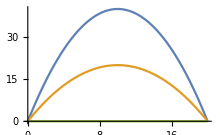

```mathematica
T1=0 (* °C *);T2=0 (* °C *);Ko=250(* W/m.°K *); L=20(* m *);
Plot[{u[x,200],u[x,100],u[x,0]},{x,0,L}]
```

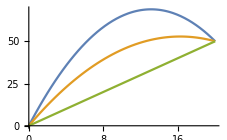

```mathematica
T1=0 (* °C *);T2=50 (* °C *);Ko=250(* W/m.°C *); L=20(* m *);(* Qo is in W *)
Plot[{u[x,200],u[x,100],u[x,0]},{x,0,L}]
```

Let’s make the plot more professional and informative.

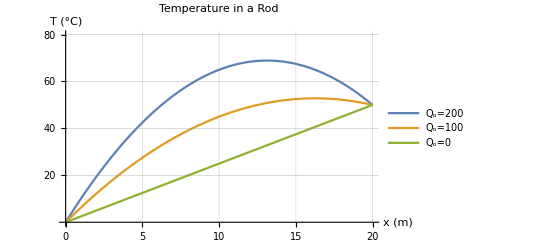

```mathematica
T1=0 (* °C *);T2=50 (* °C *);Ko=250(* W/m.°K *);L=20(* m *);
Plot[{u[x,200],u[x,100],u[x,0]},{x,0,L},PlotRange->{0,80},PlotLabel->"Temperature in a Rod", AxesLabel->{"x (m)","T (°C)"},BaseStyle->{FontSize->18},PlotStyle->Thick,Ticks->{Automatic,{20,40,60,80}},GridLines->{Automatic,{20,40,60,80}},PlotLegends->{"Q_o=200","Q_o=100","Q_o=0"}]
```